```mathematica
NotebookDirectory[]//FullForm
```

"/Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/"

### The functions and their use

```mathematica
fileName=StringJoin[NotebookDirectory[],"Sudoku.m"];
Get[fileName]
```

```mathematica
ReadSudoku[NotebookDirectory[]<>"puzzle1"]
```

{{0,0,3,0,0,0,0,5,1},{5,0,2,0,0,6,4,0,0},{0,0,7,0,5,0,0,0,0},{0,0,0,6,3,0,7,0,0},{2,0,0,7,0,8,0,0,6},{0,0,4,0,2,1,0,0,0},{0,0,0,0,7,0,8,0,0},{0,0,8,1,0,0,6,0,9},{1,7,0,0,0,0,5,0,0}}

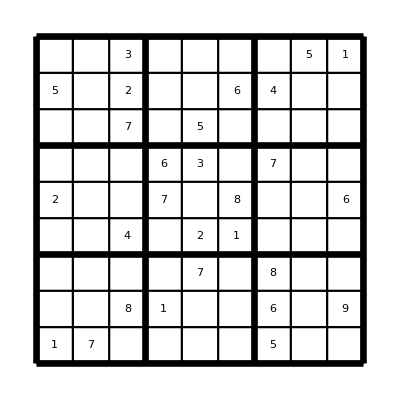

```mathematica
Show[DrawSudoku[ReadSudoku[NotebookDirectory[]<>"puzzle1"]]]
```

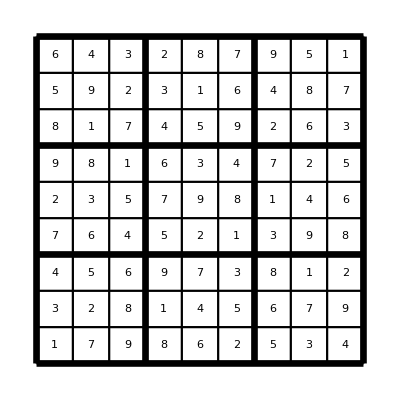

```mathematica
Show[(DrawSudoku[#1]&)/@SolveSudoku[ReadSudoku[NotebookDirectory[]<>"puzzle1"]]]
```

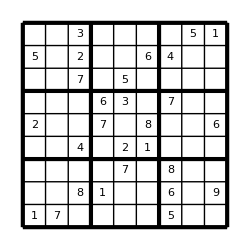

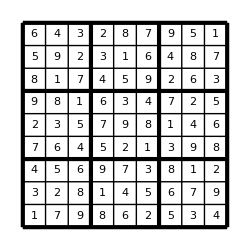

```mathematica
Show[DrawSudoku[p=ReadSudoku[NotebookDirectory[]<>"puzzle1"]]]
Show[DrawSudoku[SolveSudoku[p][[1]]]]
```

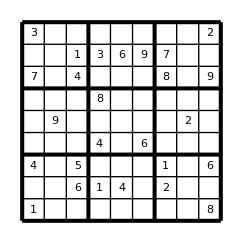

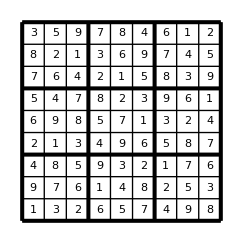

```mathematica
p=ReadSudoku[NotebookDirectory[]<>"puzzle3"];
Show[DrawSudoku[p]]
Show[DrawSudoku[SolveSudoku[p][[1]]]]
```

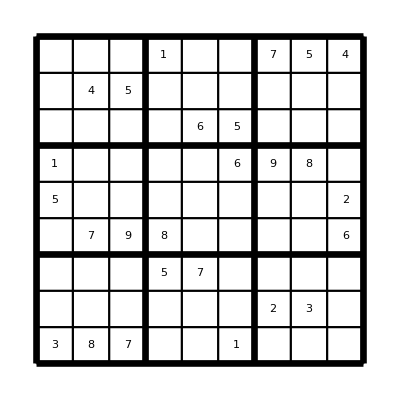

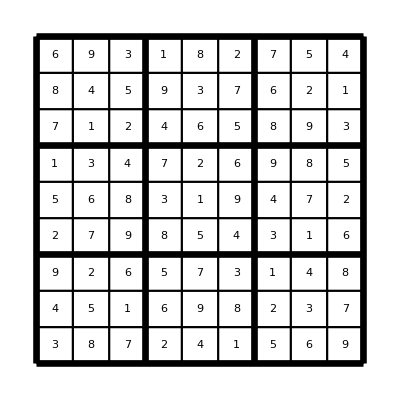

```mathematica
Show[DrawSudoku[p=ReadSudoku[NotebookDirectory[]<>"puzzle4"]]]
(Show[DrawSudoku[#1]]&)/@SolveSudoku[p]
```

```mathematica
beforeAfter[n_String]:=Module[{p},
Print["Given: ",n];
Show[DrawSudoku[p=ReadSudoku[n]]]
Print["Solution: ",n];
Show[DrawSudoku[#]]&/@SolveSudoku[p]
];
```

## All pretty patterns

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty1

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty1

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty2

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty2

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty3

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty3

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty4

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty4

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty5

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty5

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty6

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty6

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty7

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/pretty7

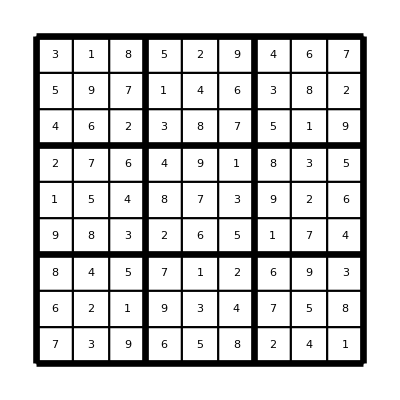
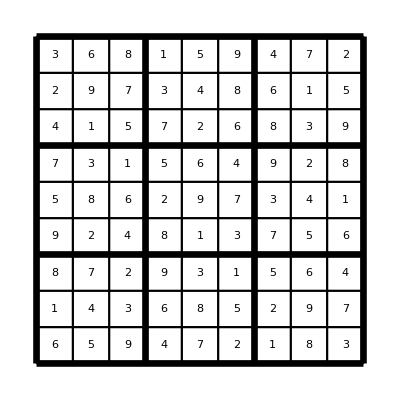
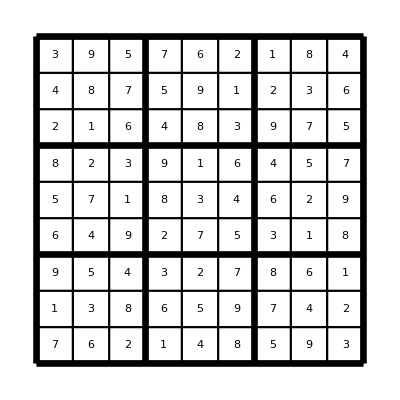
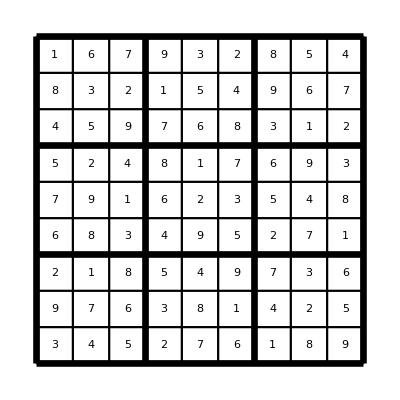
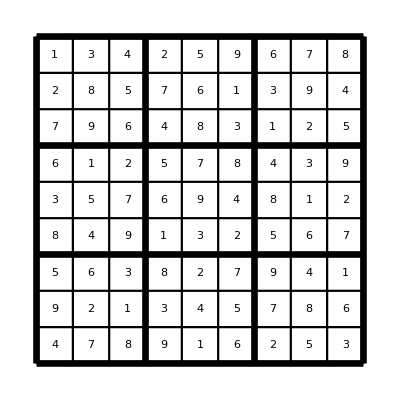
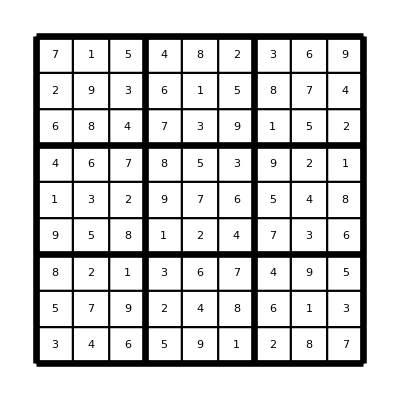
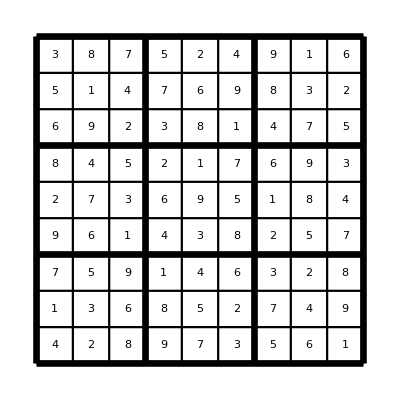

```mathematica
beforeAfter[#]&/@(NotebookDirectory[]<>"pretty"<>ToString[#]&/@Range[7])
```

## All puzzle patterns

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle1

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle1

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle2

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle2

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle3

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle3

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle4

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle4

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle5

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle5

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle6

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle6

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle7

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle7

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle8

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle8

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle9

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle9

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle10

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle10

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle11

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle11

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle12

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle12

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle13

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle13

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle14

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle14

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle15

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle15

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle16

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle16

Given: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle17

Solution: /Users/korvink1 1 2/Documents/GitHub/Mathematica/ExactCover_Soduko/puzzle17

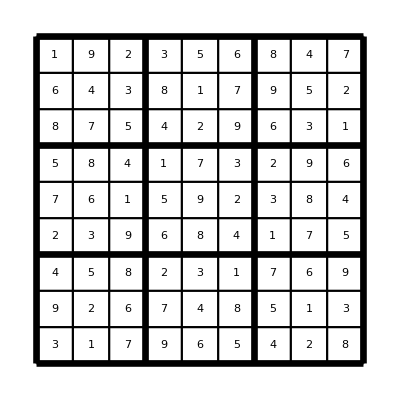
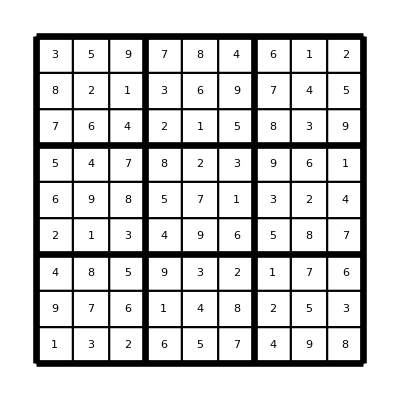
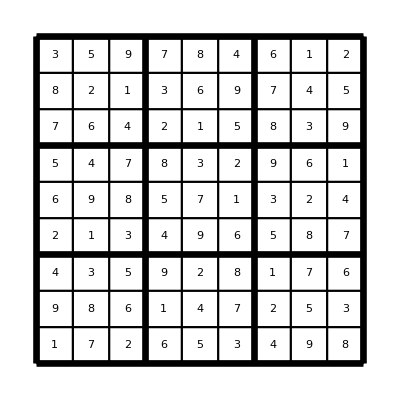
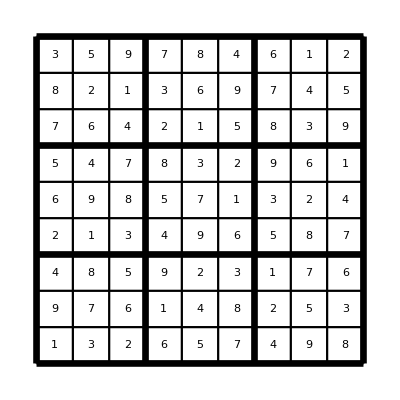
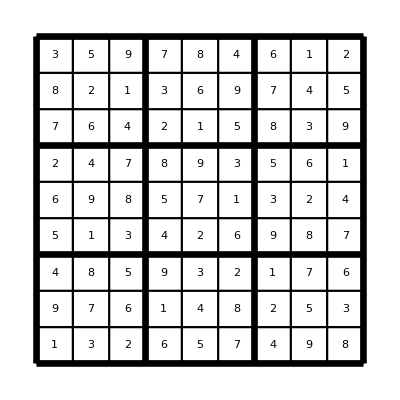
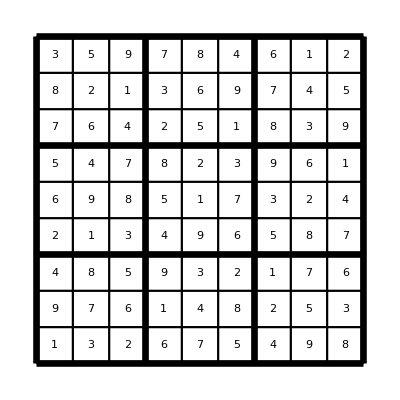
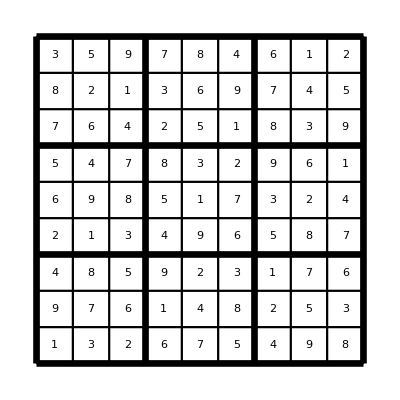
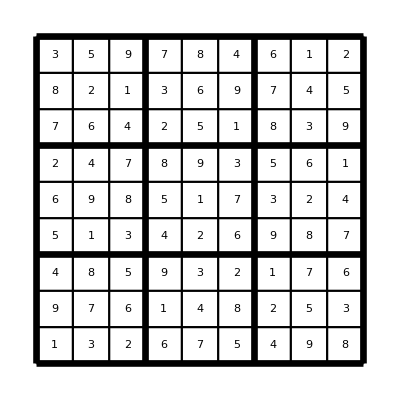
{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
beforeAfter[#]&/@(NotebookDirectory[]<>"puzzle"<>ToString[#]&/@Range[17])
```